## Metamodel

### General

```mathematica
Needs["Units`"];
print=Print;
printb=Print;
printReport[message_String]:=print[Style[ "Report : ",Darker[Green],Bold],Style[message,Darker[Green]]];
printInfo[message_String]:=print[Style[       "Info : ",Blue,Bold],Style[message,Blue]];
printWarning[message_String]:=print[Style["Warning : ",Orange,Bold],Style[message,Orange]];
printError[message_String]:=print[Style[    "Error : ",Red,Bold],Style[message,Red]];
```

### Data Import

```mathematica
importCSV[file_List]:=Module[
{startLine=8,dateformat={"Year","/","Month","/","Day"," ","Hour",":","Minute",":","Second"},

parsecsv,formattime,formatcsvrow,formatattribute,formatattributes,formatlabels,formatdata,finderrors,process,

err,importres,resindex},


parsecsv[filename_String]:=Module[{str,crit},
str=Import[filename,"String"];
crit=StringCount[str,"."]/StringCount[str,","];
If[crit>0.1,
printInfo["Correct file format"];

Return[TimeConstrained[Import[filename,"CSV"],300,printError["Import timeout, try with a smaller file"];]],
printWarning["You should export with decimal separator in English format in order to get better processing performance"];
Return[TimeConstrained[ImportString[StringReplace[StringReplace[Import[filename,"String"],{", "-> ";",","-> "."}],{";"-> ",",".."->""}],"CSV"],300,printError["Import timeout, try with a smaller file"];]]];
];

formattime[time_String]:=60*ToExpression[StringSplit[time,":"][[1]]]+ToExpression[StringSplit[time,":"][[2]]];
formatcsvrow[{date_,other___}]:={formattime[date],other};
formatattribute[attrib_String]:=
Module[{attrl,attrr,res},
If[
Length[StringPosition[attrib,"="]]>0,
attrl=StringTrim[StringSplit[attrib,"="][[1]]];
If[Length[StringSplit[attrib,"="]]≥2,
attrr=StringTrim[StringSplit[attrib,"="][[2]]];
If[attrl=="From",attrr=formattime[attrr]];
If[attrl=="To",attrr=formattime[attrr]];
If[attrl=="Date",attrr=DateList[attrr]*{1,1,1,0,0,0}];
If[attrl=="Time",attrr=DateList[attrr]*{0,0,0,1,1,1}]
,attrr=""],
attrl="softwareversion";
attrr=attrib;
];
Return[attrl-> attrr];
];
formatattributes[attrib_List]:=
Module[{res,app},
res=Map[formatattribute,attrib];
app={
"Time List"->(("Date"/.res)+ ("Time"/.res)),
"Description"-> (("Athlete"/.res) <>" "<>("EventDescription"/.res)<>" "<>DateString[(("Date"/.res)+ ("Time"/.res)),dateformat]),
"Sample Interval"-> 0.01,
"Mass"-> 340 ,
"Number"-> 1,

"Air Cx"-> 1,
"Air Velocity"->0,(*Wind speed*)
"Air Direction"->0,(*Wind coming from direction in deg *)
"Air Temperature"-> 20,(*Celsius*)
"Air Pressure"-> 101325,(*Pa*)
"Air Humidity"-> 0.5,(*relative humidity*)

"Water Cx"-> 4,
"Water Velocity"->0,(*Current speed*)
"Water Direction"->0,(*Current comming from direction in deg*)
"Water Temperature"-> 20,(*Celsius*)
"Water Salinity"->0,(*psu, nearly equal to g/kg*)

"Empirical Friction Linear Coefficient"->30,
"Empirical Friction Quadratic Coefficient"->0.4

};
Return[Join[res,app]];
];
formatlabels[label_List]:=Table[StringTrim[ToString[label[[i]]]]-> i,{i,Length[label]}];
formatdata[data_List]:=Transpose[Map[formatcsvrow,data]];
process[filename_String]:=Module[{parsedcsv,attributes,labels,data},
printInfo["Importing "<>filename];
parsedcsv=parsecsv[filename];
If[TrueQ[parsedcsv==Null],
printError["CSV Parsing problem"];
Return[{{"Description"-> "Error"}}],
attributes=formatattributes[Flatten[Take[parsedcsv,startLine-1]]];
labels=formatlabels[Flatten[Part[parsedcsv,startLine]]];
data=formatdata[Take[parsedcsv,{startLine+2,-2}]];
attributes=Append[attributes,"Length"-> Length[data[[1]]]];
printReport[("Description"/.attributes)<>" done."];
Return[{attributes,labels,data}]
]
];
finderrors[data_List]:=Module[{res},
res={};
Do[If[Not[TrueQ[("Description"/.data[[i,1]])=="Error"]],res=Append[res,data[[i]]]],{i,Length[data]}];
Return[res];
];
importres=finderrors[Map[process,file]];
resindex=Table[("Description"/.importres[[i,1]])-> i,{i,Length[importres]}];
Return[{resindex,importres}];
];
importCSV[file_String]:=importCSV[{file}];
```

### Data Extraction

```mathematica
getData[data_List]:=data[[1]];
getData[data_List,index_Integer]:=data[[2,index,2]];
getData[data_List,index_Integer,name_Integer]:=data[[2,index,3,name]];
getData[data_List,index_String]:=If[IntegerQ[index/.getData[data]],getData[data,index/.getData[data]],printError["Incorrect event name : "<>index];Interrupt[];{}];
getData[data_List,index_Integer,name_String]:=If[IntegerQ[name/.getData[data,index]],
getData[data,index,name/.getData[data,index]],
printError["Incorrect serie name : "<>name];Interrupt[];{}];
getData[data_List,index_String,name_]:=
If[IntegerQ[index/.getData[data]],
getData[data,index/.getData[data],name],
printError["Incorrect event name : "<>index];Interrupt[];{}];
getData[data_List,index_,name_List]:=Transpose[Map[getData[data,index,#]&,name]];

getAttribute[data_List,index_Integer,attname_String]:=attname/.data[[2,index,1]];
getAttribute[data_List,index_String,attname_String]:=If[IntegerQ[index/.getData[data]],getAttribute[data,index/.getData[data],attname],printError["Incorrect event name : "<>index];Interrupt[];{}];
```

```mathematica
cropData[data_List,index_Integer,delimitator_]:=Module[
{res},
res=data;
res[[2,index,3]]=Transpose[Take[Transpose[res[[2,index,3]]],delimitator]];
Return[res];
];
```

### Data processing definitions Import

```mathematica
importProcessDefinition[defin_]:=Module[{res},
printInfo["Importing data processing definitions"];
res={Table[defin[[i,1]]-> i,{i,Length[defin]}],Table[defin[[i,3]],{i,Length[defin]}],Table[defin[[i,2]],{i,Length[defin]}]};
printReport["Data processing definitions import successfull"];
Return[res];
];
```

### Data processing

```mathematica
processData[definitions_List]:=definitions[[1]];
processData[definitions_List,serie_Integer]:=definitions[[2,serie]];
processData[definitions_List,serie_String]:=
If[IntegerQ[serie/.processData[definitions]],
processData[definitions,serie/.processData[definitions]],
printError["Incorrect serie name : "<>serie]
];
processData[definitions_List,serie_,data_List,index_]:=Module[{res,newserieindex},
res=data;
(*calcul du numero d'index de la nouvelle serie*)
newserieindex=Length[res[[2,index,3]]]+1;
(*test de l'existence de la serie demandee dans le tableau de definition des series*)
If[IntegerQ[serie/.processData[definitions]],
(*mise a jour de l'index des series de la table*)
res[[2,index,2]]=Append[res[[2,index,2]],processData[definitions][[(serie/.processData[definitions]),1]]-> newserieindex];
(*mise a jour des donnees de la table, ajout de la serie*)
res[[2,index,3]]=Append[res[[2,index,3]],Apply[processData[definitions,serie],{data,index}]],
printError["Incorrect serie name : "<>serie]
];
Return[res];
];
processData[definitions_List,serie_,data_List]:=Module[{res},
res=data;
Do[res=processData[definitions,serie,res,i],{i,1,Length[getData[data]]}];
Return[res]
];
processData[definitions_List,data_List]:=Module[{res},
res=data;
printInfo["Processing data"];
Do[
printInfo["Processing "<>processData[definitions][[i,1]]];
res=processData[definitions,i,res];
printReport[processData[definitions][[i,1]]<>" processing successfull"],
{i,1,Length[processData[definitions]]}];
printReport["Data Processing successfull"];
Return[res]
];
```

### Processing utilities

```mathematica
lowpassfilter[length_Integer,cutoffperiod_]:=Module[
{res,templen,temp,distrib,freq},

Quiet[freq=N[length/(2*cutoffperiod)]];
(*distrib[n_,f_]:=If[n<f,1,0];*)
(*distrib[n_,f_]:=If[NumberQ[f],Chop[Quiet[N[Exp[-(n/f)^2]]]],1];*)

distrib[n_,f_]:=If[NumberQ[f],Chop[Quiet[N[Exp[-(n/f)^2]]]],1];

If[OddQ[length],
templen=(length-1)/2;
temp=Table[distrib[i,freq],{i,1,templen}];
res=Join[{distrib[0,freq]},temp,Reverse[temp]];
,
templen=(length-2)/2;
temp=Table[distrib[i,freq],{i,1,templen}];
res=Join[{distrib[0,freq]},temp,{distrib[templen+1,freq]},Reverse[temp]];
];
Return[res];
];
highpassfilter[length_Integer,cutoffperiod_]:=1-lowpassfilter[length,cutoffperiod];
bandpassfilter[length_Integer,{flow_,fhigh_}]:=highpassfilter[length,flow]*lowpassfilter[length,fhigh];

applylowpassfilter[series_,cutoff_]:=Module[
{padding},
padding=1000;
Return[unapplypadding[InverseFourier[Fourier[applypadding[series,padding]]*lowpassfilter[Length[series]+2*padding,cutoff]],padding]];
];
applyhighpassfilter[series_,cutoff_]:=Module[
{padding},
padding=1000;
Return[unapplypadding[InverseFourier[Fourier[applypadding[series,padding]]*highpassfilter[Length[series]+2*padding,cutoff]],padding]];
];
applybandpassfilter[series_,{cutoffl_,cutoffh_}]:=Module[
{padding},
padding=1000;
Return[unapplypadding[InverseFourier[Fourier[applypadding[series,padding]]*bandpassfilter[Length[series]+2*padding,{cutoffl,cutoffh}]],padding]];
];

applypadding[serie_,size_]:=Join[Table[serie[[1]],{size}],serie,Table[serie[[-1]],{size}]];
unapplypadding[serie_,size_]:=Take[serie,{size+1,-size-1}];

derivate[series_]:=Append[Differences[series],0]*100;
integrate[series_]:=Accumulate[series]/100;

signratio[series_] := N[Total[Map[Sign, series]]/Length[series]];

getpositive[series_] := N[Map[(# + Abs[#])/2 &, series]];
getnegative[series_] := N[Map[(# - Abs[#])/2 &, series]];

normalizelength[datatoextract_]:=
Module[{tlast=1,res={},interp},
res={};
Do[
interp=Interpolation[Transpose[{Table[N[j],{j,0,1,1/(Length[datatoextract[[i]]]-1)}],datatoextract[[i]]}]];
res=Append[res,Table[N[interp[j]],{j,0,1,1/100}]],
{i,Length[datatoextract]}
];
Return[res];
];
normalizevalues[datatoextract_]:=
Module[{tlast=1,res={},min,max},
res={};
Do[
min=Min[datatoextract[[i]]];
max=Max[datatoextract[[i]]];
res=Append[res,(datatoextract[[i]]-min)/(max-min)],
{i,Length[datatoextract]}
];
Return[res];
];
normalizeall[datatoextract_]:=normalizevalues[normalizelength[datatoextract]];
normalizeoffset[datatoextract_]:=datatoextract-datatoextract[[1]];

strokepositions[stkMark_List]:=Module[
{res},
res={};
Do[If[stkMark[[i]]==1,res=Append[res,i]],{i,Length[stkMark]}];
Return[res];
];

strokepositionsoffset[strokepositions_List,offset_,samplenumber_Integer]:=Module[
{stkpos,res},
stkpos=Join[{1},strokepositions,{samplenumber}];
res=Table[Round[(1-offset)*stkpos[[i]]+offset*stkpos[[i+1]]],{i,Length[stkpos]-1}];
Return[res]
];

timedatatostrokedata[serie_List,strokepositions_List]:=Module[
{res},
res={};
Do[res=Append[res,Take[serie,{strokepositions[[i]],strokepositions[[i+1]]}]],{i,Length[strokepositions]-1}];
Return[res]
];

strokeaggregationtotimedata[serie_List,strokepositions_List,samplenumber_Integer] := Module[
     {strokenumber,funcinterp},
     If[Length[serie] != Length[strokepositions] -1,
      printError["Stroke based series length incorrect : "<>ToString[Length[serie]]<> " ≠ "<>ToString[Length[strokepositions]-1]];
      Return[Table[-1, {i, 1, samplenumber}]],
      Quiet[
       funcinterp = Interpolation[Join[{{0, serie[[1]]}},Transpose[{Drop[strokepositions,-1], serie}], {{samplenumber+1, serie[[-1]]}}],Method->"Spline",InterpolationOrder->(2*Length[strokepositions])];
       Return[Table[N[funcinterp[i]], {i, 1, samplenumber}]]
       ]
      ]
     ];

strokedatatotimedata[serie_List,strokepositions_List,samplenumber_Integer]:=Module[
{res,interp,prev,next},

If[Length[serie] != Length[strokepositions] -1,
      printError["Stroke based series length incorrect : "<>ToString[Length[serie]]<> " ≠ "<>ToString[Length[strokepositions]-1]];
      Return[Table[-1, {i, 1, samplenumber}]],

res={};
(*lets resize elements of serie in order to be able to flatten serie later*)
next=0;
Do[
prev=next+1;
next=strokepositions[[i]];
interp=Interpolation[Transpose[{Table[N[j],{j,0,1,1/(Length[serie[[i]]]-1)}],serie[[i]]}]];
res=Append[res,Table[N[interp[j]],{j,0,1,1/(next-prev)}]];

,
{i,Length[serie]-1}
];

prev=next+1;
next=samplenumber;

interp=Interpolation[Transpose[{Table[N[j],{j,0,1,1/(Length[serie[[-1]]]-1)}],serie[[-1]]}]];
res=Append[res,Table[N[interp[j]],{j,0,1,1/(next-prev)}]];


Do[res=Join[res,Take[serie,{strokepositions[[i]],strokepositions[[i+1]]}]],{i,Length[strokepositions]-1}];
Return[res];

]
];
```

## Model

### Processing Functions

```mathematica
processdefinitions = {
{"Time Corrected",Second,sampleseriestimecorrected},

{"Forward Velocity",Meter/Second,sampleseriesforwardvel},

{"Forward Acceleration" ,  Meter/(Second^2),  sampleseriesforwardacc},
{"Up Acceleration",  Meter/(Second^2), sampleseriesupacc},
{"Right Acceleration",  Meter/(Second^2),sampleseriesrightacc},
 
{"Up Velocity",  Meter/Second,sampleseriesupvel},
{"Right Velocity" ,Meter/Second, sampleseriesrightvel},

{"Forward Distance" ,Meter,  sampleseriesforwardpos},
{"Up Distance",  Meter,sampleseriesuppos},
{"Right Distance" , Meter,sampleseriesrightpos},

{"Distance Corrected",Second,sampleseriesdistancecorrected},

{"Pitch Angular Velocity",1/Second,sampleseriespitchrot},
{"Yaw Angular Velocity",1/Second,sampleseriesyawrot},
{"Roll Angular Velocity",1/Second,sampleseriesrollrot},

{"Pitch Angle",1,sampleseriespitchangle},
{"Yaw Angle",1,sampleseriesyawangle},
{"Roll Angle",1,sampleseriesrollangle},
{"Heading Angle",1,sampleseriesheadingangle},
{"Drift Angle",1,sampleseriesdriftangle},
     
{"Pitch Angular Acceleration",1/(Second^2),sampleseriespitchacc},
{"Yaw Angular Acceleration",1/(Second^2),sampleseriesyawacc},
{"Roll Angular Acceleration",1/(Second^2),sampleseriesrollacc},

{"Water Relative Velocity",Meter/Second,sampleserieswatervel},
{"Air Relative Velocity",Meter/Second,sampleseriesairvel},

{"Water Friction Force",Newton,sampleserieswaterfrictionforce},
{"Air Friction Force",Newton,sampleseriesairfrictionforce},
{"Total Friction Force",Newton,sampleseriestotalfrictionforce},
{"Acceleration Force",Newton,sampleseriesaccelerationforce},

{"Water Friction Power",Watt,sampleserieswaterfrictionpower},
{"Air Friction Power",Watt,sampleseriesairfrictionpower},
{"Total Friction Power",Watt,sampleseriestotalfrictionpower},
{"Acceleration Power",Watt,sampleseriesaccelerationpower},
{"Total Power",Watt,sampleseriestotalpower},

{"Kinetic Energy",Joule,sampleseriescineticenergy},
{"Air Friction Energy",Joule,sampleseriesairfrictionenergy},
{"Water Friction Energy",Joule,sampleserieswaterfrictionenergy},
{"Total Friction Energy",Joule,sampleseriestotalfrictionenergy},
{"Total Energy",Joule,sampleseriestotalenergy},

{"Stroke Mark" ,  1,sampleseriesstrokemark},
{"Strokes Position" ,1,  strokeseriesstrokesposition },
{"Total Strokes" ,1,   sampleseriestotalstrokes},
     
{"Stroke" ,1/Minute,  sampleseriesstroke},

{"Distance Per Stroke",Meter,sampleseriesdistanceperstroke},
{"Forward Velocity (Stroke)" ,Meter/Second,  strokeseriesvelocity},
{"Forward Acceleration (Stroke)" ,Meter/(Second^2),  strokeseriesforward},
{"Forward Acceleration Garbage Rate (Stroke)",1,strokeseriesforwardaccgarbage},
{"Forward Acceleration Garbage Rate",1,sampleseriesforwardaccgarbage}

     };
sampleseriestimecorrected[locspec__]:=normalizeoffset[getData[locspec,"Time"]];
sampleseriesforwardacc[locspec__]:=derivate[getData[locspec,"Forward Velocity"]];
sampleseriesupacc[locspec__]:=applyhighpassfilter[getData[locspec,"Up"]*9.81,600];
sampleseriesrightacc[locspec__]:=applyhighpassfilter[getData[locspec,"Sideways"]*9.81,600];

sampleseriesforwardvel[locspec__]:=(applyhighpassfilter[integrate[applyhighpassfilter[getData[locspec,"Forward"]*9.81,60]],60]+applylowpassfilter[applylowpassfilter[getData[locspec,"Vel(Dpr)"],60],60]);
sampleseriesupvel[locspec__]:=(applyhighpassfilter[integrate[getData[locspec,"Up Acceleration"]],60])+applylowpassfilter[derivate[getData[locspec,"Up(m)"]],60];
sampleseriesrightvel[locspec__]:=applyhighpassfilter[integrate[getData[locspec,"Right Acceleration"]],60];

sampleseriesforwardpos[locspec__]:=integrate[getData[locspec,"Forward Velocity"]];
sampleseriesuppos[locspec__]:=integrate[getData[locspec,"Up Velocity"]];
sampleseriesrightpos[locspec__]:=integrate[getData[locspec,"Right Velocity"]];

sampleseriesdistancecorrected[locspec__]:=normalizeoffset[getData[locspec,"Forward Distance"]];

sampleseriespitchacc[locspec__]:= derivate[getData[locspec,"Pitch Angular Velocity"]];
sampleseriesyawacc[locspec__]:=derivate[getData[locspec,"Yaw Angular Velocity"]];
sampleseriesrollacc[locspec__]:=derivate[getData[locspec,"Roll Angular Velocity"]];

sampleseriespitchrot[locspec__]:=getData[locspec,"Gyr2(d/s)"]*π/180;
sampleseriesyawrot[locspec__]:=getData[locspec,"Gyr3(d/s)"]*π/180;
sampleseriesrollrot[locspec__]:=getData[locspec,"Gyr1(d/s)"]*π/180;

sampleseriespitchangle[locspec__]:=getData[locspec,"Pitch(deg)"]*π/180;
sampleseriesyawangle[locspec__]:=getData[locspec,"Yaw(deg)"]*π/180;
sampleseriesrollangle[locspec__]:=getData[locspec,"Roll(deg)"]*π/180;
sampleseriesheadingangle[locspec__]:=getData[locspec,"Heading"]*π/180;
sampleseriesdriftangle[locspec__]:=applylowpassfilter[applyhighpassfilter[getData[locspec,"Heading Angle"],300],20]-applyhighpassfilter[getData[locspec,"Yaw Angle"],300];


sampleserieswatervel[locspec__]:=getData[locspec,"Forward Velocity"]-getAttribute[locspec,"Water Velocity"]*Cos[getData[locspec,"Heading Angle"]-getAttribute[locspec,"Water Direction"]*π/180];

sampleseriesairvel[locspec__]:=getData[locspec,"Forward Velocity"]-getAttribute[locspec,"Air Velocity"]*Cos[getData[locspec,"Heading Angle"]-getAttribute[locspec,"Air Direction"]*π/180];


airDensity[pressure_,temperature_,humidity_]:=((1-humidity)*0.028964*pressure + humidity*0.018016*pressure)/(8.314*(273+temperature));
waterDensity[temperature_,salinity_]:=
(999.842594+0.06793952*temperature-0.009095290*temperature^2+0.0001001685*temperature^3-0.000001120083*temperature^4+0.000000006536332*temperature^5)+
(0.824493-0.0040899*temperature+0.000076438*temperature^2-0.00000082467*temperature^3+0.0000000053875*temperature^4)*salinity+(-0.00572466+0.00010227*temperature-0.0000016546*temperature^2)*salinity^(3/2)+0.00048314*salinity^2;

sampleserieswaterfrictionforce[locspec__]:=0.5*waterDensity[getAttribute[locspec,"Water Temperature"],getAttribute[locspec,"Water Salinity"]]*getAttribute[locspec,"Water Cx"]*Map[#^2&,getData[locspec,"Water Relative Velocity"]];
sampleseriesairfrictionforce[locspec__]:=0.5*airDensity[getAttribute[locspec,"Air Pressure"],getAttribute[locspec,"Air Temperature"],getAttribute[locspec,"Air Humidity"]]*getAttribute[locspec,"Air Cx"]*Map[#^2&,getData[locspec,"Air Relative Velocity"]];
sampleseriestotalfrictionforce[locspec__]:=
getAttribute[locspec,"Empirical Friction Linear Coefficient"]*getData[locspec,"Water Relative Velocity"] + getAttribute[locspec,"Empirical Friction Quadratic Coefficient"]*Map[#^2&,getData[locspec,"Water Relative Velocity"]];
sampleseriesaccelerationforce[locspec__]:=getData[locspec,"Forward Acceleration"]*getAttribute[locspec,"Mass"];

sampleserieswaterfrictionpower[locspec__]:=getData[locspec,"Forward Velocity"]*getData[locspec,"Water Friction Force"];
sampleseriesairfrictionpower[locspec__]:=getData[locspec,"Forward Velocity"]*getData[locspec,"Air Friction Force"];
sampleseriestotalfrictionpower[locspec__]:=getData[locspec,"Forward Velocity"]*getData[locspec,"Total Friction Force"];
sampleseriesaccelerationpower[locspec__]:=getData[locspec,"Forward Velocity"]*getData[locspec,"Acceleration Force"];

sampleseriescineticenergy[locspec__]:=0.5*getAttribute[locspec,"Mass"]*Map[#^2&,getData[locspec,"Forward Velocity"]];
sampleseriesairfrictionenergy[locspec__]:=Accumulate[getData[locspec,"Air Friction Power"]]*getAttribute[locspec,"Sample Interval"];
sampleserieswaterfrictionenergy[locspec__]:=Accumulate[getData[locspec,"Water Friction Power"]]*getAttribute[locspec,"Sample Interval"];
sampleseriestotalfrictionenergy[locspec__]:=Accumulate[getData[locspec,"Total Friction Power"]]*getAttribute[locspec,"Sample Interval"];

(*
accelerationpower[velocity_,acceleration_]:=mass*acceleration*velocity;
frictionpower[velocity_,acceleration_]:=1*velocity^2+5*velocity^3;
totalpower[velocity_,acceleration_]:=accelerationpower[velocity,acceleration]+frictionpower[velocity,acceleration];
power[velocity_,acceleration_]:=totalpower[velocity,acceleration]/number;
applylowpassfilter[power[getData[dataproc,1,"Forward Velocity"],getData[dataproc,1,"Forward Acceleration"]],200];*)

sampleseriestotalpower[locspec__]:=getData[locspec,"Total Friction Power"]+getData[locspec,"Acceleration Power"];
sampleseriestotalenergy[locspec__]:=getData[locspec,"Total Friction Energy"]+getData[locspec,"Kinetic Energy"];
sampleseriesstrokemark[locspec__]:=getData[locspec,"StkMark"];
sampleseriestotalstrokes[locspec__]:={};
sampleseriesstroke[locspec__]:={};
sampleseriesdistanceperstroke[locspec__]:={};
strokeseriesstrokesposition[locspec__]:=strokepositionsoffset[strokepositions[getData[locspec,"Stroke Mark"]],0.55,getAttribute[locspec,"Length"]];
strokeseriesvelocity[locspec__]:=timedatatostrokedata[getData[locspec,"Forward Velocity"],getData[locspec,"Strokes Position"]];
strokeseriesforward[locspec__]:=timedatatostrokedata[getData[locspec,"Forward Acceleration"],getData[locspec,"Strokes Position"]];
strokeseriesforwardaccgarbage[locspec__]:=Module[{strokes,meanstroke,res},
strokes=normalizeall[getData[locspec,"Forward Acceleration (Stroke)"]];
meanstroke=Mean[strokes];
res=Table[N[Variance[strokes[[i]]-meanstroke]],{i,Length[strokes]}];
res[[1]]=0;
res[[-1]]=0;
Return[res];
];
sampleseriesforwardaccgarbage[locspec__]:=applylowpassfilter[strokeaggregationtotimedata[getData[locspec,"Forward Acceleration Garbage Rate (Stroke)"],getData[locspec,"Strokes Position"],getAttribute[locspec,"Length"],1]];
```

## Import

### Import

```mathematica
FileNameSetter[Dynamic[filesnames]]
```

```mathematica
Dynamic[filesnames]
```

```mathematica
(*filesnames=FileNames["*.csv",NotebookDirectory[]];
filesnames=FileNames["*.csv","/Users/vincent/Desktop/MathematicaMinimax/Temple/Vitesse vq4"];
filesnames={"/Users/vincent/Desktop/MathematicaMinimax/Coupes du monde/K2 (Colin - Lecrubier) 6037 201105191140.csv"};
filesnames={
"K4-1000m-2013/Etalon/K4 1_2 Finale Player 6105 201306141805 Arrivee.csv",
"/Users/Vincent/Documents/Minimax/K4-1000m-2013/Etalon/K4 Série Player 6105 201306141435 Arrivee.csv"};*)


dataimport=importCSV[filesnames];
procdef=importProcessDefinition[processdefinitions];
dataproc=processData[procdef,dataimport];
```

Set::partw: Part 1 of {} does not exist.

Set::partw: Part -1 of {} does not exist.

Fourier::fftl: Argument {{} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), « 35 », {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), {} ⟦ -1 ⟧ - 0.999736\ ({} ⟦ -1 ⟧ - 1.\ {} ⟦ 1 ⟧), « 5743 »} is not a non-empty list or rectangular array of numeric quantities.

InverseFourier::fftl: Argument {1.\ Fourier[{{} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), « 36 », {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), {} ⟦ -1 ⟧ - 0.999736\ (Part[« 2 »] + Times[« 2 »]), « 5743 »}], « 19 »\ « 1 », « 47 », 0, « 5743 »} is not a non-empty list or rectangular array of numeric quantities.

Take::take: Cannot take positions 1001 through -1001 in InverseFourier[{1.\ Fourier[{{} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], « 32 », {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], {} ⟦ -1 ⟧ - 0.999736\ Plus[« 2 »], « 5743 »}], 0.957998\ « 7 »[« 1 »], « 48 », « 5743 »}].

```mathematica
getData[dataimport]
```

{K4 Série Player  2013/06/14 14:35:00→1,K4 1/2 Finale Player  2013/06/14 18:05:29→2,K4 H V_C_E_M WC3 Poznan FA K4H 1000M 2013/06/01 11:27:13→3,K4 H V_C_E_M WC3 Poznan serie K4H 1000M vt face 2013/05/31 10:28:49→4,K4 H C_V_E_M WC2 Racice FA K4 1000M 2013/05/18 11:28:56→5,K4 C_V_E_M WC2 Racice K4 1000m série 2013/05/17 12:18:57→6,K4 Série Player  2013/06/14 14:35:00→7,K4 1/2 Finale Player  2013/06/14 18:05:29→8,Vincent LECRUBIER WC3 Poznan serie K1H 1000M vt face 2013/05/31 09:32:19→9,Vincent LECRUBIER WC3 Poznan FA K1H 1000M 2013/06/01 10:28:10→10}

```mathematica
getData[dataproc,1]
```

{Time→1,Lap Counter→2,Forward→3,Sideways→4,Sideways(m/s)→5,Up→6,Up(m)→7,Stroke→8,Vel(Dpr)→9,Vel(100hz)→10,Vel/Stk→11,VLo/Stk→12,VHi/Stk→13,Gyr1(d/s)→14,Gyr2(d/s)→15,Gyr3(d/s)→16,Roll(deg)→17,Pitch(deg)→18,Yaw(deg)→19,Heading→20,#sats→21,Altitude→22,Vel(av)→23,HDOP→24,VDOP→25,Dist(dgps)→26,Plyr.Load(Raw)→27,Ac3HR→28,AcFlt1(g)→29,AcFlt2(g)→30,AcFlt3(g)→31,Mag Fwd→32,Mag Left→33,Mag Up→34,StkMark→35,Odometer→36,Longitude→37,Latitude→38,Heart Rate→39,Acc(dpr)→40,Estimate XY→41,Fig. of Merit→42,Facing→43,AoA→44,Raw Vel.→45,Smooth Vel.→46,Plyr.Ld(2D Accum)→47,Plyr.Ld(2D)→48,Plyr.Ld(slow)→49,Exertion Index→50,E.I.Accum→51,Debug1→52,Debug2→53,Debug3→54,Debug4→55,Debug5→56,Debug6→57,Debug7→58,Debug8→59,Tackle Load→60,Vel ()→61,H.R. ()→62,Possession→63,PlyrLd(smooth)→64,Plyr. Load→65,HR Exertion→66,Plyr Ld 1D(Fwd)→67,Plyr Ld 1D(Side)→68,Plyr Ld 1D(Up)→69,CVE→70,IMU-forward→71,IMU-sideways→72,IMU-up→73,IMU-roll→74,IMU-pitch→75,IMU-yaw→76,Aux Channel 07→77,Aux Channel 08→78,Aux Channel 09→79,Aux Channel 10→80,Aux Channel 11→81,IMU-resultant→82,GPS Time→83,GPS Latitude→84,GPS Longitude→85,GPS Info→86,GPS Flags→87,GPS SigStr→88,GPS Sat Elev→89,GPS Sat Azim→90,→91,Time Corrected→92,Forward Velocity→93,Forward Acceleration→94,Up Acceleration→95,Right Acceleration→96,Up Velocity→97,Right Velocity→98,Forward Distance→99,Up Distance→100,Right Distance→101,Distance Corrected→102,Pitch Angular Velocity→103,Yaw Angular Velocity→104,Roll Angular Velocity→105,Pitch Angle→106,Yaw Angle→107,Roll Angle→108,Heading Angle→109,Drift Angle→110,Pitch Angular Acceleration→111,Yaw Angular Acceleration→112,Roll Angular Acceleration→113,Water Relative Velocity→114,Air Relative Velocity→115,Water Friction Force→116,Air Friction Force→117,Total Friction Force→118,Acceleration Force→119,Water Friction Power→120,Air Friction Power→121,Total Friction Power→122,Acceleration Power→123,Total Power→124,Kinetic Energy→125,Air Friction Energy→126,Water Friction Energy→127,Total Friction Energy→128,Total Energy→129,Stroke Mark→130,Strokes Position→131,Total Strokes→132,Stroke→133,Distance Per Stroke→134,Forward Velocity (Stroke)→135,Forward Acceleration (Stroke)→136,Forward Acceleration Garbage Rate (Stroke)→137,Forward Acceleration Garbage Rate→138}

### Verifications

#### Forward

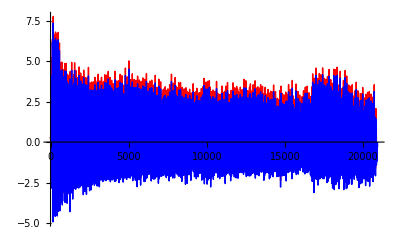

```mathematica
ListPlot[{
getData[dataproc,1,"Forward"]*9.81,
getData[dataproc,1,"Forward Acceleration"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

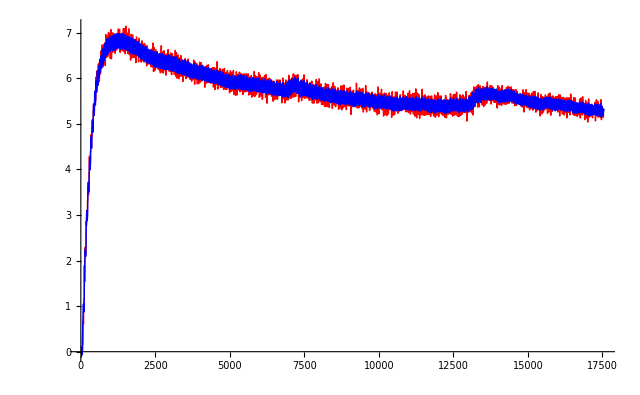

```mathematica
ListPlot[{
getData[dataproc,1,"Vel(Dpr)"],
getData[dataproc,1,"Forward Velocity"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

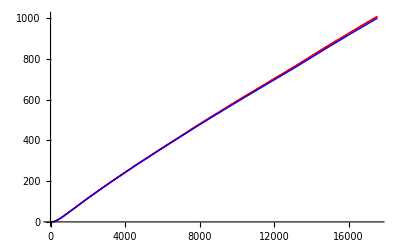

```mathematica
ListPlot[{
getData[dataproc,1,"Odometer"]-getData[dataproc,1,"Odometer"][[1]],
getData[dataproc,1,"Forward Distance"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

#### Right

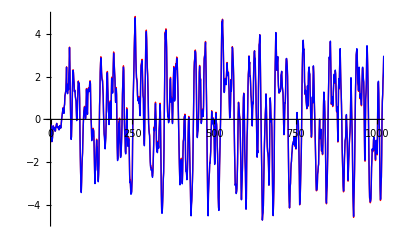

```mathematica
ListPlot[{
getData[dataproc,1,"Sideways"]*9.81,
getData[dataproc,1,"Right Acceleration"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,1000},All}]
```

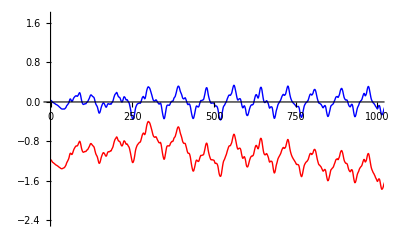

```mathematica
ListPlot[{
getData[dataproc,1,"Sideways(m/s)"],
getData[dataproc,1,"Right Velocity"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,1000},All}]
```

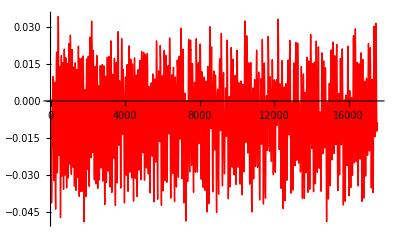

```mathematica
ListPlot[{
getData[dataproc,1,"Right Distance"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

#### Up

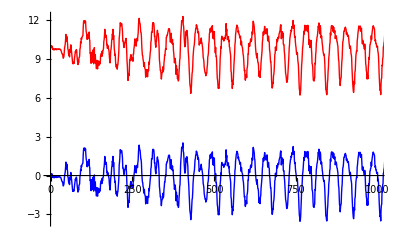

```mathematica
ListPlot[{
getData[dataproc,1,"Up"]*9.81,
getData[dataproc,1,"Up Acceleration"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,1000},All}]
```

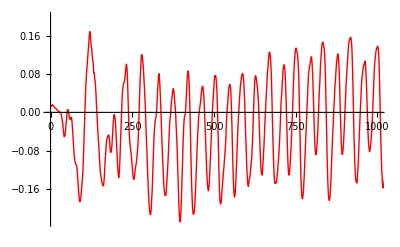

```mathematica
ListPlot[{
getData[dataproc,1,"Up Velocity"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,1000},All}]
```

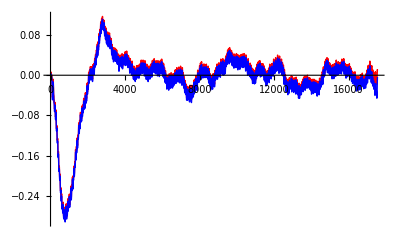

```mathematica
ListPlot[{
getData[dataproc,1,"Up(m)"],
getData[dataproc,1,"Up Distance"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

#### Pitch

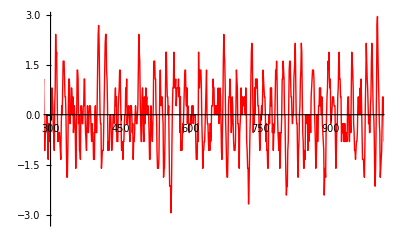

```mathematica
ListPlot[{
getData[dataproc,1,"Pitch Angular Acceleration"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{300,1000},All}]
```

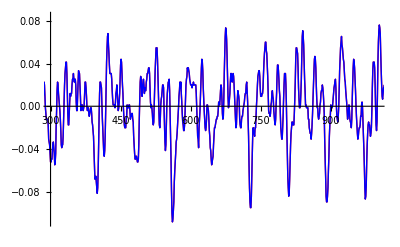

```mathematica
ListPlot[{
getData[dataproc,1,"Gyr2(d/s)"]*π/180,
getData[dataproc,1,"Pitch Angular Velocity"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{300,1000},All}]
```

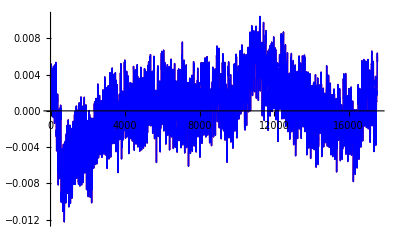

```mathematica
ListPlot[{
getData[dataproc,1,"Pitch(deg)"]*π/180,
getData[dataproc,1,"Pitch Angle"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

#### Yaw

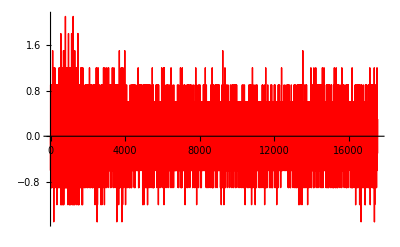

```mathematica
ListPlot[{
getData[dataproc,1,"Yaw Angular Acceleration"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

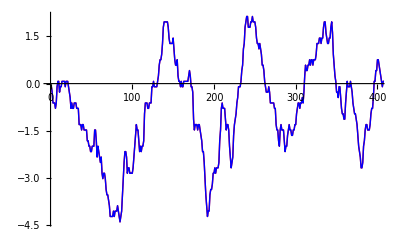

```mathematica
ListPlot[{
getData[dataproc,1,"Gyr3(d/s)"],
getData[dataproc,1,"Yaw Angular Velocity"]*180/π
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,400},All}]
```

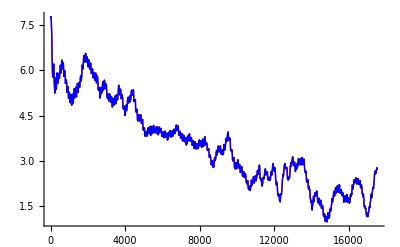

```mathematica
ListPlot[{
getData[dataproc,1,"Yaw(deg)"],
getData[dataproc,1,"Yaw Angle"]*180/π
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

#### Roll

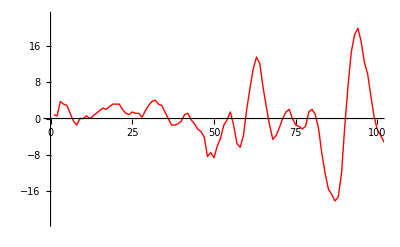

```mathematica
ListPlot[{
getData[dataproc,1,"Roll Angular Acceleration"]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,100},All}]
```

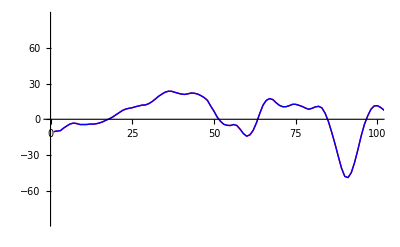

```mathematica
ListPlot[{
getData[dataproc,1,"Gyr1(d/s)"],
getData[dataproc,1,"Roll Angular Velocity"]*180/π
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,100},All}]
```

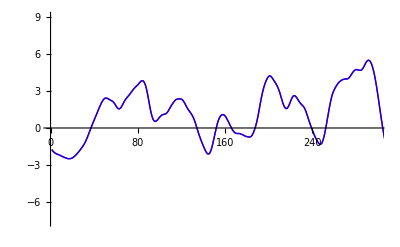

```mathematica
ListPlot[{
getData[dataproc,1,"Roll(deg)"],
getData[dataproc,1,"Roll Angle"]*180/π
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,300},All}]
```

#### Heading

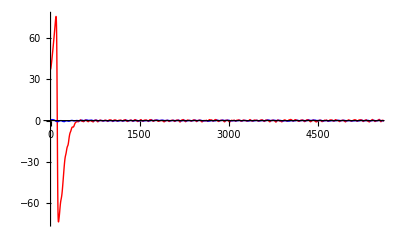

```mathematica
ListPlot[{
applylowpassfilter[applyhighpassfilter[getData[dataproc,1,"Heading Angle"]*180/π,300],20],
applyhighpassfilter[getData[dataproc,1,"Yaw Angle"]*180/π,300]
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{{0,5500},All}]
```

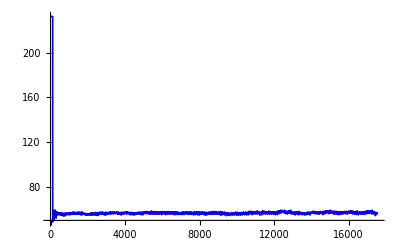

```mathematica
ListPlot[{
getData[dataproc,1,"Heading"],
getData[dataproc,1,"Heading Angle"]*180/π
},
PlotStyle->{Red,Blue},Joined-> True,PlotRange->{All,All}]
```

### Other

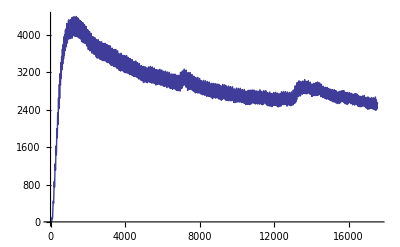

```mathematica
ListPlot[
getData[dataproc,1,"Cinetic Energy"]
,Joined->True,PlotRange->{All,{0,All}}]
```

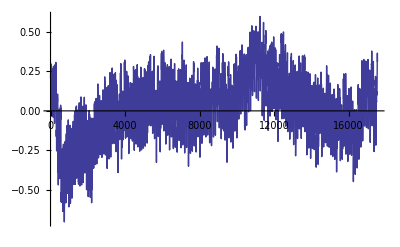

```mathematica
ListPlot[
getData[dataproc,1,"Pitch Angle"]*180/π
,Joined->True,PlotRange->{All,All}]
```

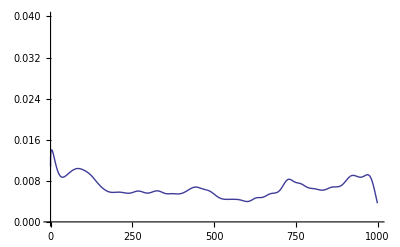

```mathematica
ListPlot[
getData[dataproc,1,{"Distance Corrected","Forward Acceleration Garbage Rate"}]
,Joined->True,PlotRange->{All,{0,0.04}}]
```

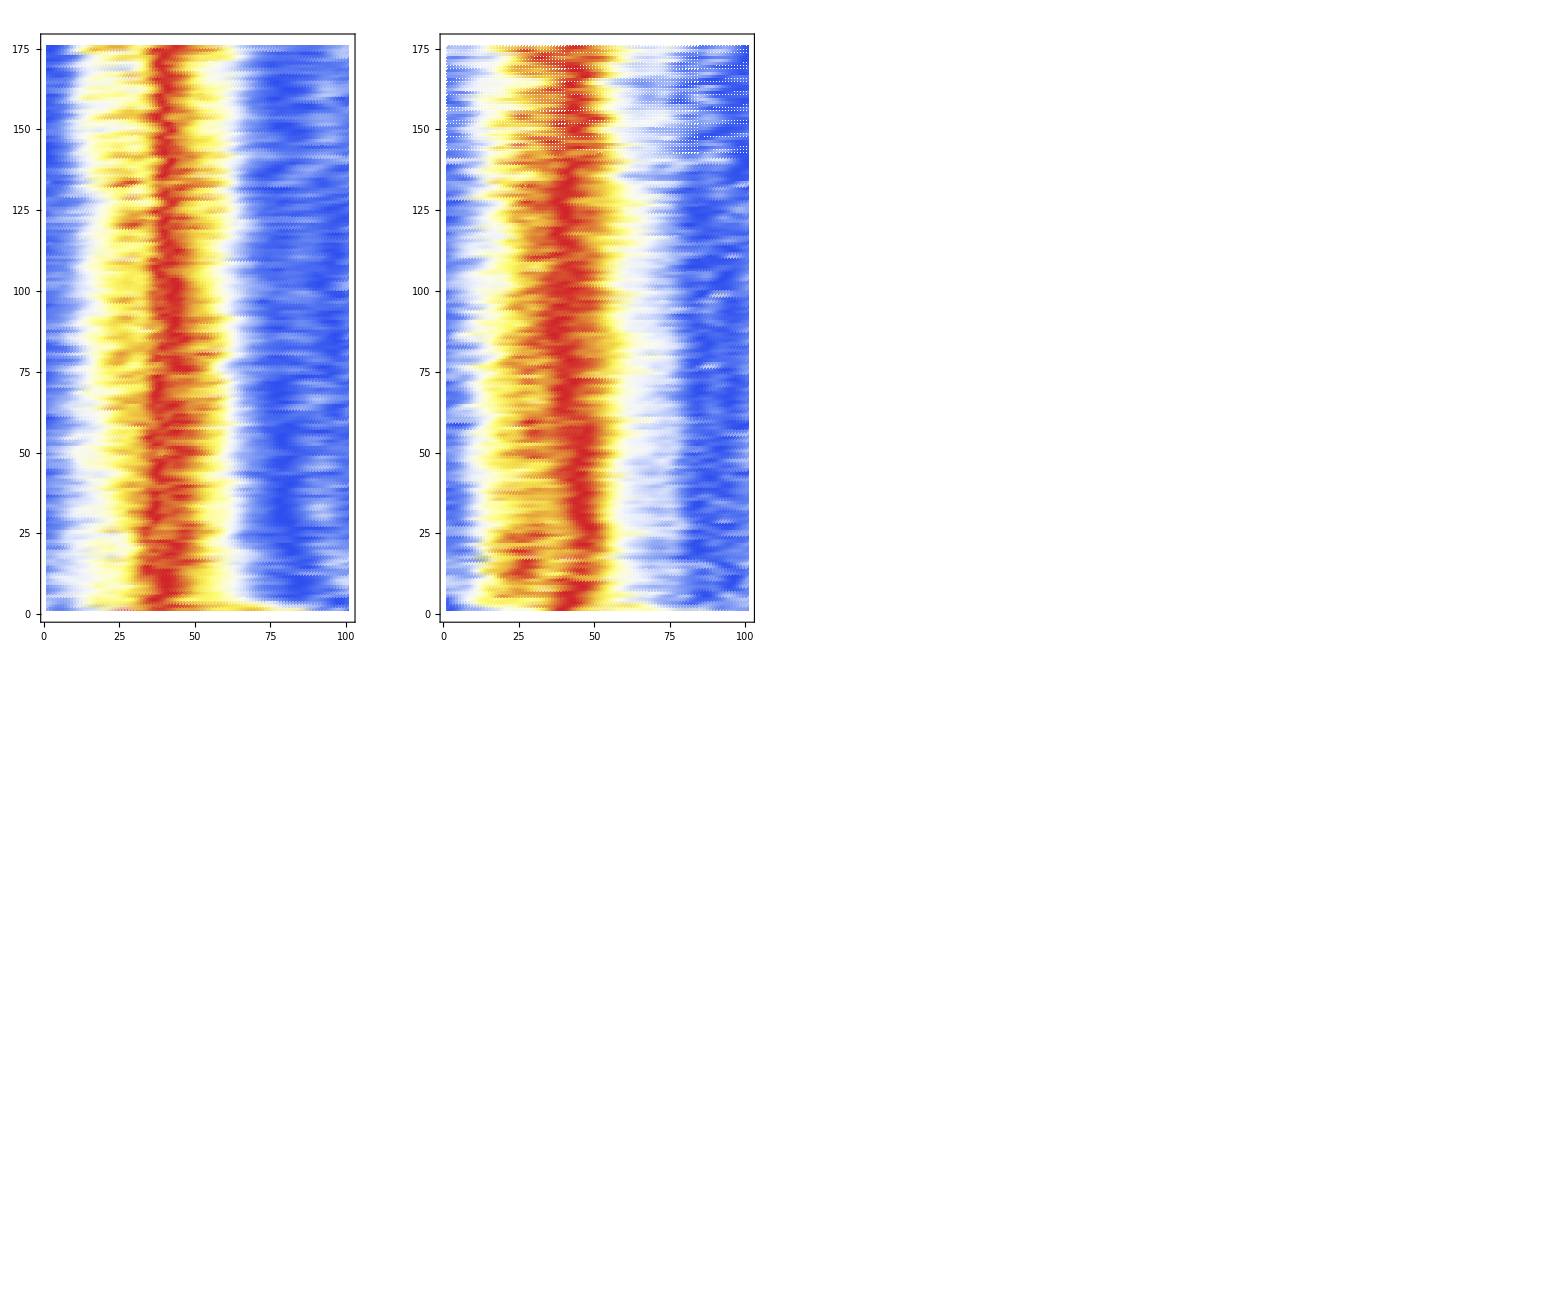

```mathematica
Module[{dat,datg,datd,assym},
dat=normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ dat]/300,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ dat]/300,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datg-datd,ImageSize->{400,600},AspectRatio->Length[ dat]/300,ColorFunction-> "TemperatureMap"],
ListPlot[assym,ImageSize->{400,600},AspectRatio->Length[ dat]/300,Joined->True]
},
{
ListPlot[Mean[datg],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datd],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datg-datd],ImageSize->{400,400},Joined->True],
0
}}
]
]
```

```mathematica
ListDensityPlot[normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]],ImageSize->{400,800},AspectRatio->Length[ getData[dataproc,1,"Forward Acceleration (Stroke)"]]/150,ColorFunction-> "TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot[normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]],Joined->True]
```

-Graphics-

```mathematica
ListPlot[normalizeall[getData[dataproc,1,"Forward Velocity (Stroke)"]],Joined->True]
```

-Graphics-

```mathematica
processData[definitions_List,name_String,data_List,index_]:=If[IntegerQ[name/.getData[data]],
getData[data,index/.getData[data],name],
printError["Incorrect event name : "<>index];Interrupt[];{}];
processData[definitions_List]:=Table[definitions[[i,1]]-> i,{i,Length[definitions]}];
```

```mathematica
Needs["Units`"];
processData[data_List] := Module[
   {
    
    },

   
   strokemarkidentifier = 1;
   
   processdefinitions = {
{"Forward Acceleration" ,  Meter/(Second^2),  sampleseriesforwardacc},
{"Up Acceleration",  Meter/(Second^2), sampleseriesupacc},
{"Right Acceleration",  Meter/(Second^2),sampleseriesrightacc},
 
{"Forward Velocity",Meter/Second,sampleseriesforwardvel},
{"Up Velocity",  Meter/Second,sampleseriesupvel},
{"Right Velocity" ,Meter/Second, sampleseriesrightvel},

{"Forward Distance" ,Meter,  sampleseriesforwardpos},
{"Up Distance",  Meter,sampleseriesuppos},
{"Right Distance" , Meter,sampleseriesrightpos},
     
{"Pitch Angular Acceleration",1/(Second^2),sampleseriespitchacc},
{"Yaw Angular Acceleration",1/(Second^2),sampleseriesyawacc},
{"Roll Angular Acceleration",1/(Second^2),sampleseriesrollacc},

{"Pitch Angular Velocity",1/Second,sampleseriespitchrot},
{"Yaw Angular Velocity",1/Second,sampleseriesyawrot},
{"Roll Angular Velocity",1/Second,sampleseriesrollrot},

{"Pitch Angle",1,sampleseriespitchangle},
{"Yaw Angle",1,sampleseriesyawangle},
{"Roll Angle",1,sampleseriesrollangle},
{"Heading Angle",1,sampleseriesheadingangle},
{"Drift Angle",1,sampleseriesdriftangle},

{"Water Relative Velocity",Meter/Second,sampleserieswaterspeed},
{"Air Relative Velocity",Meter/Second,sampleserieswaterspeed},

{"Water Friction Force",Newton,sampleserieswaterfrictionforce},
{"Air Friction Force",Newton,sampleseriesaierfrictionforce},
{"Acceleration Force",Newton,sampleseriesaccelerationforce},

{"Water Friction Power",Watt,sampleserieswaterfrictionpower},
{"Air Friction Power",Watt,sampleseriesairfrictionpower},
{"Acceleration Power",Watt,sampleseriesaccelerationpower},

{"Cinetic Energy",Joule,sampleseriescineticenergy},
{"Air Friction Energy",Joule,sampleseriesairfrictionenergy},
{"Water Friction Energy",Joule,sampleseriesairfrictionenergy},
{"Total Energy",Joule,sampleseriestotalenergy},

{"Stroke Mark" ,  1,sampleseriesstrokemark},
{"Total Strokes" ,1,   sampleseriestotalstrokes},
     
{"Stroke" ,1/Minute,  sampleseriesstroke},

{"Distance Per Stroke",Meter,sampleseriesdistanceperstroke},
{"Strokes Position" ,1,  strokeseriesstrokesposition },
{"Velocity (Stroke)" ,Meter/Second,  strokeseriesstrokesposition}

     };
 
   

   
   strokeposition[stknumber_Integer] := Module[
     {temp},
     temp = Position[seriesstrokenumber[], stknumber];
     If[Length[temp] >= 1, Return[temp[[1, 1]]], Return[[0]]];
     ];
   
   strokepositionlist[] := Module[
     {res, stk},
     res = {1};
     stk = getData[data, index, "StkMark"];
     Do[If[stk[[i]] == strokemarkidentifier, res = Append[res, i]], {i, 1, samplenumber}];
     Return[res];
     ];
   
   
   seriesstrokenumber[] := Module[{n = 1, res = {}, stk},
     stk = getData[data, index, "StkMark"];
     Do[
      If[stk[[i]] == strokemarkidentifier, n = n + 1];
      res = Append[res, n],
      {i, 1, samplenumber}
      ];
     Return[res];
     ];
   
   
   strokesplit[series_List] :=
    Module[{tlast = 1, res = {}, stkmark, datatoextract},
     stkmark = getData[data, index, "StkMark"];
     datatoextract = series;
     Do[
      If[stkmark[[i]] == strokemarkidentifier,
       res = N[Append[res, Take[datatoextract, {tlast, i}]]];
       tlast = i;
       ],
      {i, 1, Length[stkmark]}
      ];
     res = Append[res, N[Take[datatoextract, {tlast, Length[datatoextract]}]]];
     Return[res];
     ];
   
   
   seriesforwarddutycycle[] := (stroketotime[Map[signratio, strokesplit[getData[data, index, "Forward"]]]] + 1)/2;
   
   seriesveldutycycle[] := (stroketotime[Map[signratio, strokesplit[ seriesvelbias[]  ]]] + 1)/2;
   
   seriesmaxaccel[] := stroketotime[Map[Max, strokesplit[seriesfwdcorrected[]]]];
   seriesmaxdecel[] := stroketotime[-1*Map[Min, strokesplit[seriesfwdcorrected[]]]];
   
   seriesvelcorrected[] := Module[
     {cutoff, padding, vdpr, tfvdpr, v100hz, tfv100hz, res, tfres},
     cutoff = 100;
     padding = 500;
     
     vdpr = getData[data, index, "Vel(Dpr)"];
     
     (*v100hz=getData[data,index,"Vel(100hz)"];*)
v100hz = integrate[InverseFourier[Fourier[getData[data, index, "Forward"]/9.81]*highpassfilter[samplenumber, cutoff]]];
     
     vdpr = applypadding[vdpr, padding];
     v100hz = applypadding[v100hz, padding];
     
     tfvdpr = Fourier[vdpr];
     tfv100hz = Fourier[v100hz];
     tfvdpr = tfvdpr*lowpassfilter[samplenumber + 2*padding, cutoff];
     tfv100hz = tfv100hz*highpassfilter[samplenumber + 2*padding, cutoff];
     tfres = tfvdpr + tfv100hz;
     res = InverseFourier[tfres];
     
     res = unapplypadding[res, padding];
     Return[res];
     ];
   
   seriesfwdcorrected[] := derivate[seriesvelcorrected[]]*9.81;
   seriesodometercorrected[] := integrate[seriesvelcorrected[]]/100.;
   seriesvelaverage[] := applylowpassfilter[seriesvelcorrected[], 300];
   seriesvelbias[] := seriesvelcorrected[] - seriesvelaverage[];
   
   
   zerocrossings[series_] := Append[Differences[Map[Sign, series]], 0];
   seriesstkmarkcorrected[] := Module[
     {rawzerocrossings, rawzerocrossingspos, acceldat, crossingintervals, crossingintervalsdif, thresh, temptodel, res, offset1, offset2},
     rawzerocrossings = zerocrossings[seriesvelbias[]];
     rawzerocrossingspos = Transpose[Join[Position[rawzerocrossings, 2], Position[rawzerocrossings, 1]]][[1]];
     crossingintervals = Differences[rawzerocrossingspos];
     crossingintervalsdif = Differences[crossingintervals];
     thresh = 3*N[StandardDeviation[crossingintervalsdif]];
     temptodel = {};
     Do[If[crossingintervalsdif[[i]] >= thresh,
       temptodel = Append[temptodel, i];
       ],
      {i, 1, Length[crossingintervalsdif]}];
     
     res = rawzerocrossings;
     offset1 = 0;
     offset2 = 0;
     
     Do[
      If[((temptodel[[i]] + offset1) >= 1 ) && ((temptodel[[i]] + offset1) <= Length[rawzerocrossingspos]) ,
       If[((rawzerocrossingspos[[temptodel[[i]] + offset1]] + offset2) >= 1) && ((rawzerocrossingspos[[temptodel[[i]] + offset1]] + offset2) <= Length[res]),
        res[[rawzerocrossingspos[[temptodel[[i]] + offset1]] + offset2]] = 0;
        ]
       ]
      ,
      {i, 1, Length[temptodel]}
      ];
     
     Return[getpositive[res]];
     ];
   
   seriesstrokecorrected[] := Module[
     {stk, res, last, val, timek},
     
     stk = seriesstkmarkcorrected[];
     timek = getData[data, index, "Time"];
     
     last = 0;
     val = 1;
     res = Table[0, {samplenumber}];
     Do[
      If[stk[[i]] > 0,
       val = timek[[i]] - last;
       last = timek[[i]];
       ];
      res[[i]] = val;
      , {i, 1, samplenumber}];
     res = N[60./res];
     Return[res];
     ];
   
   
   samplenumber = Length[getData[data, index, 1]];
   strokenumber = Length[getDataStroke[data, index, "StkMark"]];
   
   
   labelsbase = {
     };
   
   labels = Table[ labelsbase[[i]] -> seriesnumber + i, {i, 1, Length[labelsbase]}];
   
   resultbase = {
     };
   
   
   Table[processData[data, i], {i, Length[data]}];
   
   result = data[[index]];
   result[[2]] = Join[result[[2]], labels];
   result[[3]] = Join[result[[3]], resultbase];
   
   Print["Traitement de " <> ("Description" /. data[[index, 1]]) <> " reussi"];
   Return[result];
   ];
```

### Other

```mathematica
Module[{dat},
dat=getData[dataimport,1,"Vel(Dpr)"];
Manipulate[
ListPlot[Take[dat,{Min[i,j],Max[i,j]}],Joined->True,PlotRange-> {All,{0,8}}]
,{{i,1},1,Length[dat]},{{j,Length[dat]},1,Length[dat]}]
]
```

Take::normal: Nonatomic expression expected at position 1 in Take[dat$6294, {1, 17552}].

ListPlot::lpn: Take[dat$6294, {1, 17552}] is not a list of numbers or pairs of numbers.

```mathematica
ListPlot[
{
applylowpassfilter[getData[dataimport,1,"Vel(Dpr)"],1000]/7,
applylowpassfilter[0.5+0.5*Map[Sign,getData[dataimport,1,"Forward"]],1000]
},
PlotRange->{All,{0,1}}]
```

-Graphics-

### Functions collection

#### Convolution (Tres lent)

```mathematica
kernelcinfinity[klen_]:=Module[
{res},
res=Table[Exp[-1/(1-x^2)],{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelsinusoidal[klen_]:=Module[
{res},
res=Table[Cos[Pi*x]/2+1/2,{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelsinc[klen_]:=Module[
{res},
res=Table[Sinc[Pi*x],{x,-10+2/klen,10-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kerneltriangular[klen_]:=Module[
{res},
res=Table[1-Abs[x],{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelrectangular[klen_]:=Module[
{res},
res=Table[1,{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelcinfinityflat[klen_]:=Module[
{res},
res=Table[Exp[-1/(1-x^2)]^(1/4),{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelpast[klen_]:=Module[
{res},
res=Table[UnitStep[x]*Exp[-10*x],{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelfuture[klen_]:=Module[
{res},
res=Table[UnitStep[-x]*Exp[10*x],{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
kernelponctual[klen_]:=Module[
{res},
res=Table[If[x≥ -1/klen&&x≤ 1/klen,1,0],{x,-1+2/klen,1-2/klen,2/klen}];
res=res/Total[res];
Return[res];
];
Smooth[datal_List,kershape_,kerlen_]:=
Module[{dat,klen,ker,paddlist},
klen=Round[kerlen,2];
ker=N[kershape[klen]];
klen=Length[ker]+1;
dat=N[datal];
paddlist=N[Table[UnitStep[i],{i,-Length[datal]-kerlen,Length[datal]+kerlen}]*(datal[[1]]-datal[[-1]])+datal[[-1]]];
Return[ListConvolve[ker,dat,{klen/2,-klen/2},paddlist]];
];
```

#### Filtrage frequentiel (Rapide)

```mathematica
lowpassfilter[length_Integer,cutoffperiod_]:=Module[
{res,templen,temp,distrib,freq},

Quiet[freq=N[length/(2*cutoffperiod)]];
(*distrib[n_,f_]:=If[n<f,1,0];*)
distrib[n_,f_]:=If[NumberQ[f],Chop[Quiet[N[Exp[-(n/f)^2]]]],1];

If[OddQ[length],
templen=(length-1)/2;
temp=Table[distrib[i,freq],{i,1,templen}];
res=Join[{distrib[0,freq]},temp,Reverse[temp]];
,
templen=(length-2)/2;
temp=Table[distrib[i,freq],{i,1,templen}];
res=Join[{distrib[0,freq]},temp,{distrib[templen+1,freq]},Reverse[temp]];
];
Return[res];
];
highpassfilter[length_Integer,cutoffperiod_]:=1-lowpassfilter[length,cutoffperiod];
bandpassfilter[length_Integer,{flow_,fhigh_}]:=highpassfilter[length,flow]*lowpassfilter[length,fhigh];

applypadding[serie_,size_]:=Join[Table[serie[[1]],{size}],serie,Table[serie[[-1]],{size}]];
unapplypadding[serie_,size_]:=Take[serie,{size+1,-size-1}];

derivate[series_]:=Append[Differences[series],0];
integrate[series_]:=Accumulate[series];

applylowpassfilter[series_,cutoff_]:=Module[
{padding},
padding=1000;
Return[unapplypadding[InverseFourier[Fourier[applypadding[series,padding]]*lowpassfilter[Length[series]+2*padding,cutoff]],padding]];
];
applyhighpassfilter[series_,cutoff_]:=Module[
{padding},
padding=1000;
Return[unapplypadding[InverseFourier[Fourier[applypadding[series,padding]]*highpassfilter[Length[series]+2*padding,cutoff]],padding]];
];
applybandpassfilter[series_,{cutoffl_,cutoffh_}]:=Module[
{padding},
padding=1000;
Return[unapplypadding[InverseFourier[Fourier[applypadding[series,padding]]*bandpassfilter[Length[series]+2*padding,{cutoffl,cutoffh}]],padding]];
];

 signratio[series_] := N[Total[Map[Sign, series]]/Length[series]];
```

## Rapports

### Assymétrie

```mathematica
Module[{dat,datg,datd,assym},
dat=normalizeall[getData[dataproc,6,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datg-datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListPlot[assym,ImageSize->{400,600},AspectRatio->Length[ dat]/200,Joined->True]
},
{
ListPlot[Mean[datg],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datd],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datg-datd],ImageSize->{400,400},Joined->True],
0
}}
]
]
```

```mathematica
Module[{dat,datg,datd,assym},
dat=normalizeall[getData[dataproc,6,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datg-datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListPlot[assym,ImageSize->{400,600},AspectRatio->Length[ dat]/200,Joined->True]
},
{
ListPlot[Mean[datg],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datd],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datg-datd],ImageSize->{400,400},Joined->True],
0
}}
]
]
```

-Graphics-

```mathematica
harmonicsPower[data_]:=Module[{datg,transg,noiseg},
datg=normalizeall[data];
transg=normalizevalues[Abs[Map[FourierDCT,datg]]];
noiseg=Transpose[{Table[i,{i,Length[datg]}],applylowpassfilter[Map[Norm,transg[[All,2;;]]]/transg[[All,1]],2]}];
Return[noiseg]
]
ListPlot[{harmonicsPower[getData[dataproc,7,"Forward Acceleration (Stroke)"]],
harmonicsPower[getData[dataproc,8,"Forward Acceleration (Stroke)"]],
harmonicsPower[getData[dataproc,3,"Forward Acceleration (Stroke)"]],
harmonicsPower[getData[dataproc,4,"Forward Acceleration (Stroke)"]],
harmonicsPower[getData[dataproc,5,"Forward Acceleration (Stroke)"]],
harmonicsPower[getData[dataproc,6,"Forward Acceleration (Stroke)"]]},PlotStyle->{Red,Yellow,Green,Cyan,Blue,Magenta},Joined->True,PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

-Graphics-

```mathematica
getData[dataproc]
```

{K4 Série Player  2013/06/14 14:35:00→1,K4 1/2 Finale Player  2013/06/14 18:05:29→2,K4 H V_C_E_M WC3 Poznan FA K4H 1000M 2013/06/01 11:27:13→3,K4 H V_C_E_M WC3 Poznan serie K4H 1000M vt face 2013/05/31 10:28:49→4,K4 H C_V_E_M WC2 Racice FA K4 1000M 2013/05/18 11:28:56→5,K4 C_V_E_M WC2 Racice K4 1000m série 2013/05/17 12:18:57→6}

```mathematica
Module[{datg,datd,transg,transd,noiseg,noised},
datg=Take[normalizeall[getData[dataproc,3,"Forward Acceleration (Stroke)"]],{1,-1,2}];
datd=Take[normalizeall[getData[dataproc,3,"Forward Acceleration (Stroke)"]],{2,-1,2}];
transg=normalizevalues[Abs[Map[FourierDCT,datg]]];
noiseg=Transpose[{applylowpassfilter[Map[Norm,transg[[All,2;;]]]/transg[[All,1]],4],Table[i,{i,Length[datg]}]}];
transd=normalizevalues[Abs[Map[FourierDCT,datd]]];
noised=Transpose[{applylowpassfilter[Map[Norm,transd[[All,2;;]]]/transd[[All,1]],4],Table[i,{i,Length[datd]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ datg]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ datg]/200,ColorFunction-> "TemperatureMap"],
ListPlot[{noiseg,noised},ImageSize->{400,600},AspectRatio->Length[ datg]/200,Joined->True]
}}
]
]
```

-Graphics-

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,2,"Forward Acceleration"],getData[dataproc,2,"Forward Velocity"]-5.5}],{0.001,0.001},ColorFunction->"TemperatureMap",PlotRange->{{-3,4},{-1,3}}]
```

-Graphics-

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,2,"Pitch Angle"],getData[dataproc,2,"Forward Acceleration"]}],{0.0001,0.001},ColorFunction->"TemperatureMap",PlotRange->{{-0.01,0.01},{-3,4}}]
```

-Graphics-

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,1,"Pitch Angle"],getData[dataproc,1,"Forward Acceleration"]}],{0.00005,0.01},ColorFunction->"TemperatureMap",PlotRange->{{-0.01,0.01},{-3.,5.}}]
```

-Graphics-

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,1,"Roll Angle"],getData[dataproc,1,"Forward Acceleration"]}],{0.001,0.01},ColorFunction->"TemperatureMap",PlotRange->{{-0.2,0.2},{-3.,5.}}]
SmoothDensityHistogram[Transpose[{getData[dataproc,2,"Roll Angle"],getData[dataproc,2,"Forward Acceleration"]}],{0.001,0.01},ColorFunction->"TemperatureMap",PlotRange->{{-0.2,0.2},{-3.,5.}}]
```

-Graphics-

-Graphics-

```mathematica
Export["/Users/Vincent/Downloads/K4 H C_V_E_M 6108 201305181128 K4H1000M FA.avi",
Table[
Show[


SmoothDensityHistogram[

Take[Transpose[{getData[dataproc,1,"Roll Angle"],getData[dataproc,1,"Forward Acceleration"]}],
{x,x+1000}]
,{0.005,0.05},ColorFunction->"TemperatureMap",PlotRange->{{-0.2,0.2},{-3.,5.}}]


,

Graphics[Text[
ToString[Round[getData[dataproc,1,"Forward Distance"][[x]]]]<>" m",{0,5.5},{0,0}]],

PlotRange->{{-0.2,0.2},{-3.,6.}}

],

{x,1,Length[getData[dataproc,1,"Roll Angle"]]-1000,10}
]]
```

/Users/Vincent/Downloads/K4 H C_V_E_M 6108 201305181128 K4H1000M FA.avi

```mathematica
ListPlot[
{
Transpose[{getData[dataproc,1,"Forward Distance"],getData[dataproc,1,"Forward Velocity"]}],
Transpose[{getData[dataproc,2,"Forward Distance"],getData[dataproc,2,"Forward Velocity"]}]
},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{{0,100},{0,7}}]
```

-Graphics-

```mathematica
Manipulate[ListPlot[
{getData[dataproc,1,"Forward Velocity"],
Take[getData[dataproc,2,"Forward Velocity"],{deb2,-1}],
Take[getData[dataproc,1,"Forward Velocity"],{deb3,-1}]
},Joined->True,PlotStyle->{Red,Green,Blue},PlotRange->{0,7}],
{deb2,1,400,1},{deb3,1,400,1}]
```

```mathematica
ListPlot[{applylowpassfilter[getData[dataproc,1,"Total Friction Force"],10]},PlotRange->All]
```

-Graphics-

```mathematica
getAttribute[dataproc,1,"Mass"]
```

90

```mathematica
Module[{a,b,fit},
fit=FindFit[Transpose[{getData[dataproc,1,"Forward Velocity"],-getAttribute[dataproc,1,"Mass"]*getData[dataproc,1,"Forward Acceleration"]}],a*v+b*v^2,{a,b},v];
Print["Empirical Friction Linear Coefficient"->(a/.fit)];
Print["Empirical Friction Quadratic Coefficient"->(b/.fit)];

];
```

Empirical Friction Linear Coefficient→7.9211

Empirical Friction Quadratic Coefficient→0.101846

```mathematica
ListPlot[{

applylowpassfilter[getData[dataproc,2,"Forward Velocity"],1000]
}

,PlotStyle->{Red,Blue,Green},Joined->True,PlotRange->{All,{0,8}}]
```

-Graphics-

```mathematica
SmoothDensityHistogram[Transpose[{applylowpassfilter[ Abs[getData[dataproc,2,"Roll Angular Velocity"]]+10*Abs[getData[dataproc,2,"Roll Angle"]],10],applylowpassfilter[getData[dataproc,2,"Forward Velocity"],10]}],{0.001,0.01},ColorFunction->"TemperatureMap",PlotRange->{{0.,2},{0.,8.}}]
```

-Graphics-

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Acceleration Power"],200]}],
Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Friction Power"],200]}],
Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]

ListPlot[
{

Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Acceleration Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Friction Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]

ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
getData[dataproc]
```

{K4 Série Player  2013/06/14 14:35:00→1,K4 1/2 Finale Player  2013/06/14 18:05:29→2,K4 H V_C_E_M WC3 Poznan FA K4H 1000M 2013/06/01 11:27:13→3,K4 H V_C_E_M WC3 Poznan serie K4H 1000M vt face 2013/05/31 10:28:49→4,K4 H C_V_E_M WC2 Racice FA K4 1000M 2013/05/18 11:28:56→5,K4 C_V_E_M WC2 Racice K4 1000m série 2013/05/17 12:18:57→6,K4 Série Player  2013/06/14 14:35:00→7,K4 1/2 Finale Player  2013/06/14 18:05:29→8,Vincent LECRUBIER WC3 Poznan serie K1H 1000M vt face 2013/05/31 09:32:19→9,Vincent LECRUBIER WC3 Poznan FA K1H 1000M 2013/06/01 10:28:10→10}

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,3,"Forward Distance"],
applylowpassfilter[getData[dataproc,3,"Total Power"],200]}],
Transpose[{getData[dataproc,4,"Forward Distance"],
applylowpassfilter[getData[dataproc,4,"Total Power"],200]}],
Transpose[{getData[dataproc,5,"Forward Distance"],
applylowpassfilter[getData[dataproc,5,"Total Power"],200]}]

},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{All,All},PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

-Graphics-

```mathematica
n=1;
f=20;
ListPlot[
{
Transpose[{getData[dataproc,n,"Forward Distance"],
applylowpassfilter[getData[dataproc,n,"Total Power"],f]}],
Transpose[{getData[dataproc,n,"Forward Distance"],
applylowpassfilter[getData[dataproc,n,"Acceleration Power"],f]}],
Transpose[{getData[dataproc,n,"Forward Distance"],
applylowpassfilter[getData[dataproc,n,"Total Friction Power"],f]}]
},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{{0,200},All}]
```

-Graphics-

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}],
Transpose[{getData[dataproc,3,"Forward Distance"],
applylowpassfilter[getData[dataproc,3,"Total Power"],200]}],
Transpose[{getData[dataproc,4,"Forward Distance"],
applylowpassfilter[getData[dataproc,4,"Total Power"],200]}],
Transpose[{getData[dataproc,5,"Forward Distance"],
applylowpassfilter[getData[dataproc,5,"Total Power"],200]}],
Transpose[{getData[dataproc,6,"Forward Distance"],
applylowpassfilter[getData[dataproc,6,"Total Power"],200]}]

},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{All,All},PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

-Graphics-

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,3,"Forward Distance"],
applylowpassfilter[getData[dataproc,3,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,4,"Forward Distance"],
applylowpassfilter[getData[dataproc,4,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,5,"Forward Distance"],
applylowpassfilter[getData[dataproc,5,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,6,"Forward Distance"],
applylowpassfilter[getData[dataproc,6,"Forward Velocity"],200]}]

},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{All,All},PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

-Graphics-

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[power[getData[dataproc,1,"Forward Velocity"],getData[dataproc,1,"Forward Acceleration"]],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[power[getData[dataproc,2,"Forward Velocity"],getData[dataproc,2,"Forward Acceleration"]],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]
```

```mathematica
TableForm[getData[dataproc]]
```

K4 Série Player  2013/06/14 14:35:00→1
K4 1/2 Finale Player  2013/06/14 18:05:29→2
K4 H V_C_E_M WC3 Poznan FA K4H 1000M 2013/06/01 11:27:13→3
K4 H V_C_E_M WC3 Poznan serie K4H 1000M vt face 2013/05/31 10:28:49→4
K4 H C_V_E_M WC2 Racice FA K4 1000M 2013/05/18 11:28:56→5
K4 C_V_E_M WC2 Racice K4 1000m série 2013/05/17 12:18:57→6
K4 Série Player  2013/06/14 14:35:00→7
K4 1/2 Finale Player  2013/06/14 18:05:29→8
Vincent LECRUBIER WC3 Poznan serie K1H 1000M vt face 2013/05/31 09:32:19→9
Vincent LECRUBIER WC3 Poznan FA K1H 1000M 2013/06/01 10:28:10→10

```mathematica
n=8;
GraphicsGrid[{Table[
DensityHistogram[Transpose[{

applylowpassfilter[getData[dataproc,n,"Roll Angle"],1],applylowpassfilter[getData[dataproc,n,"Forward Acceleration"],1]

}],{100,100},ColorFunction->"TemperatureMap",PlotRange->All,ImageSize->{320,320}],{n,3,6}],
Table[
DensityHistogram[Transpose[{

applylowpassfilter[getData[dataproc,n,"Roll Angle"],1],applylowpassfilter[getData[dataproc,n,"Forward Acceleration"],1]

}],{100,100},ColorFunction->"TemperatureMap",PlotRange->All,ImageSize->{320,320}],{n,7,10}]
}]
```

-Graphics-

```mathematica
getData[dataproc]
```

{K4 Série Player  2013/06/14 14:35:00→1,K4 1/2 Finale Player  2013/06/14 18:05:29→2,K4 H V_C_E_M WC3 Poznan FA K4H 1000M 2013/06/01 11:27:13→3,K4 H V_C_E_M WC3 Poznan serie K4H 1000M vt face 2013/05/31 10:28:49→4,K4 H C_V_E_M WC2 Racice FA K4 1000M 2013/05/18 11:28:56→5,K4 C_V_E_M WC2 Racice K4 1000m série 2013/05/17 12:18:57→6,K4 Série Player  2013/06/14 14:35:00→7,K4 1/2 Finale Player  2013/06/14 18:05:29→8,Vincent LECRUBIER WC3 Poznan serie K1H 1000M vt face 2013/05/31 09:32:19→9,Vincent LECRUBIER WC3 Poznan FA K1H 1000M 2013/06/01 10:28:10→10}

```mathematica
n=6;
xdat=getData[dataproc,n,"Roll Angle"]*180/π;
ydat1=applylowpassfilter[getData[dataproc,n,"Total Friction Power"],1];
ydat2=applylowpassfilter[getData[dataproc,n,"Acceleration Power"],1];
ydat3=applylowpassfilter[getData[dataproc,n,"Total Power"],1];
dur=(getData[dataproc,n,"Time"][[-1]]-getData[dataproc,n,"Time"][[1]]);

Animate[ListPlot[
{
Transpose[{Take[xdat,{i,i+20}],Take[ydat1,{i,i+20}]}],
Transpose[{Take[xdat,{i,i+20}],Take[ydat2,{i,i+20}]}],
Transpose[{Take[xdat,{i,i+20}],Take[ydat3,{i,i+20}]}]
}
,Joined->True,PlotStyle->{Red,Darker[Green],Blue},PlotRange->{{-12,12},{-8000,10000}},ImageSize->{640,480}],{i,1,Length[xdat-20],1},DefaultDuration->dur]
```

```mathematica
normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]]
```

```mathematica
"Forward Acceleration Garbage Rate"
```

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Forward Acceleration Garbage Rate"],2]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Forward Acceleration Garbage Rate"],2]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]
```

-Graphics-

```mathematica
x="Forward Velocity";
y="Right Velocity";
z="Up Velocity";
n=70;
cutoff=100;


serie1=1;
serie2=2;
serie3=3;

xmin=Min[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
xmax=Max[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
ymin=Min[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
ymax=Max[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
zmin=Min[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];
zmax=Max[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];

xmin=-0.3;
xmax=0.3;
ymin=-0.3;
ymax=0.3;
zmin=-0.3;
zmax=0.3;


ref=Table[1,{n},{n},{n}];

res1=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie1,x],cutoff],
applyhighpassfilter[getData[dataproc,serie1,y],cutoff],
applyhighpassfilter[getData[dataproc,serie1,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res1=res1/Max[res1];


res2=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie2,x],cutoff],
applyhighpassfilter[getData[dataproc,serie2,y],cutoff],
applyhighpassfilter[getData[dataproc,serie2,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res2=res2/Max[res2];


res3=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie3,x],cutoff],
applyhighpassfilter[getData[dataproc,serie3,y],cutoff],
applyhighpassfilter[getData[dataproc,serie3,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res3=res3/Max[res3];

res=Outer[Times,res1,{10,0,0,0}]+Outer[Times,res2,{0,10,0,0}]+Outer[Times,res3,{0,0,10,0}]+Outer[Times,res1^2+res2^2+res3^2,{0,0,0,5}];

Image3D[res,Background->Black]
```

-Graphics3D-

```mathematica
x="Forward Acceleration";
y="Roll Angle";
z="Right Acceleration";
n=70;
cutoff=100;


serie1=4;
serie2=5;
serie3=6;

xmin=Min[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
xmax=Max[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
ymin=Min[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
ymax=Max[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
zmin=Min[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];
zmax=Max[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];
(*
xmin=-1;
xmax=1;
ymin=-0.3;
ymax=0.3;
zmin=-0.3;
zmax=0.3;
*)


ref=Table[1,{n},{n},{n}];

res1=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie1,x],cutoff],
applyhighpassfilter[getData[dataproc,serie1,y],cutoff],
applyhighpassfilter[getData[dataproc,serie1,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res1=res1/Max[res1];


res2=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie2,x],cutoff],
applyhighpassfilter[getData[dataproc,serie2,y],cutoff],
applyhighpassfilter[getData[dataproc,serie2,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res2=res2/Max[res2];


res3=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie3,x],cutoff],
applyhighpassfilter[getData[dataproc,serie3,y],cutoff],
applyhighpassfilter[getData[dataproc,serie3,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res3=res3/Max[res3];

res=Outer[Times,res1,{10,0,0,0}]+Outer[Times,res2,{0,10,0,0}]+Outer[Times,res3,{0,0,10,0}]+Outer[Times,res1^2+res2^2+res3^2,{0,0,0,1}];

Image3D[res,Background->Black]
With[{i=Image3D[res],size=n},
Manipulate[Grid[{#&/@{Show[Image3DSlices[i,{s},1][[1]],Graphics[{Red,Line[{{c,0},{c,size}}],Line[{{0,size-r+1},{size,size-r+1}}]}],ImageSize->{320,320}],
Show[Image3DSlices[i,{r},2][[1]],Graphics[{Red,Line[{{c,0},{c,size}}],Line[{{0,size-s+1},{size,size-s+1}}]}],ImageSize->{320,320}],
Show[Image3DSlices[i,{c},3][[1]],Graphics[{Red,Line[{{r,0},{r,size}}],Line[{{0,size-s+1},{size,size-s+1}}]}],ImageSize->{320,320}]}}],
{s,1,size,1},{r,1,size,1},{c,1,size,1}]]
```

-Graphics3D-

```mathematica
VectorPlot3D
```

```mathematica
ListVectorPlot3D[
Take[
Transpose[
{
{
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Forward Velocity"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Right Velocity"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Up Velocity"],cutoff]]
},{
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Forward Acceleration"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Right Acceleration"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Up Acceleration"],cutoff]]
}
},
{2,3,1}
]
,
{1000,1100}
],
VectorPoints->10,
PlotRange->All
]
```

-Graphics3D-

```mathematica
Plot3D[Max[res1,res2],{res1,0,1},{res2,0,1}]
Plot3D[Min[res1,res2],{res1,0,1},{res2,0,1}]
Plot3D[1-(1-res1)*(1-res2),{res1,0,1},{res2,0,1}]
Plot3D[res1*res2,{res1,0,1},{res2,0,1}]
Plot3D[res1^2+res2^2,{res1,0,1},{res2,0,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
x="Forward Acceleration";
y="Right Acceleration";
z="Up Acceleration";
f="Forward Velocity";
serie=1;
opacity=0.5;
ListContourPlot3D[Transpose[{
Standardize[getData[dataproc,serie,x]],
Standardize[getData[dataproc,serie,y]],
getData[dataproc,serie,z],
power[getData[dataproc,serie,"Forward Velocity"],getData[dataproc,serie,"Forward Acceleration"]]
}],Contours->6,Mesh->None,BoundaryStyle->None,ContourStyle->{Opacity[opacity,Red],Opacity[opacity,Yellow],Opacity[opacity,Green],Opacity[opacity,Cyan],Opacity[opacity,Blue],Opacity[opacity,Magenta]},PlotRange->All,MaxPlotPoints->100,AxesLabel->{x,y,z}]
```

```mathematica
x="Pitch Angular Velocity";
y="Roll Angular Velocity";
z="Yaw Angular Velocity";
```

```mathematica
x="Forward Acceleration";
y="Right Acceleration";
z="Up Acceleration";
f="Forward Acceleration";
serie=1;
ListContourPlot3D[Transpose[{
Standardize[getData[dataproc,serie,x]],
Standardize[getData[dataproc,serie,y]],
Standardize[getData[dataproc,serie,z]],
Standardize[getData[dataproc,serie,f]]
}],Contours->6,Mesh->None,ContourStyle->{Red,Yellow,Green,Cyan,Blue,Magenta},PlotRange->All,MaxPlotPoints->80,AxesLabel->{x,y,z}]
```

```mathematica
x="Roll Angle";
y="Pitch Angle";
z="Yaw Angle";
f="Forward Acceleration";
serie=1;
ListContourPlot3D[Transpose[{
Standardize[getData[dataproc,serie,x]],
Standardize[getData[dataproc,serie,y]],
Standardize[getData[dataproc,serie,z]],
Standardize[getData[dataproc,serie,f]]
}],Contours->6,Mesh->None,ContourStyle->{Red,Yellow,Green,Cyan,Blue,Magenta},PlotRange->All,MaxPlotPoints->80,AxesLabel->{x,y,z}]
```

```mathematica
Plot[(1-Cos[x])/2,{x,0,2*π}]
```

-Graphics-

```mathematica
f1[x_]:=(((1-Cos[x])/2)^8)*2-0.3;
f2[x_]:=((1-Cos[x])/2)^0.2-0.3;
Plot[{f1[x],f2[x]},{x,0,2*π}]
```

-Graphics-